```mathematica
$Assumptions=ϵ ∈ Reals && ϵ1 ∈ Reals && ϕ ∈ Reals && γl∈ Reals && γr∈ Reals && t0 ∈ Reals
Assumptions->$Assumptions
```

ϵ∈ℝ&&ϵ1∈ℝ&&ϕ∈ℝ&&γl∈ℝ&&γr∈ℝ&&t0∈ℝ

Assumptions→ϵ∈ℝ&&ϵ1∈ℝ&&ϕ∈ℝ&&γl∈ℝ&&γr∈ℝ&&t0∈ℝ

```mathematica
Id =IdentityMatrix[4];
ME= ϵ Id //Simplify;


MH = ({{ϵ1, ts, 0, t}, {t, ϵ1, ts, 0}, {0, t, ϵ1, ts}, {ts, 0, t, ϵ1}});
MΓ= ({{γl, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, γr, 0}, {0, 0, 0, 0}});

MΓL= ({{γl, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}});
MΓR= ({{0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, γr, 0}, {0, 0, 0, 0}});


t=E^(I ϕ) t0;
ts= E^ (-I ϕ) t0;


MGr = ME - MH  + I MΓ/2;
MGa = ME - MH  - I MΓ/2;

(* to see the matrices
*)
(*ME - MH  + I MΓ/2//MatrixForm
ME - MH  - I MΓ/2//MatrixForm*)

retarded_GF

MGr1=MGr/Det[MGr] ;
Inverse[MGr1] //Simplify //MatrixForm          ;
Gr1= Inverse[MGr1] //Simplify;
Gr=1/Det[MGr]  Gr1;
Det[MGr]           ;


advanced_GF

MGa1=MGa/Det[MGa] ;
Inverse[MGa1] //Simplify //MatrixForm       ;
Ga1= Inverse[MGa1] //Simplify;
Ga=1/Det[MGa]  Ga1;
Det[MGa]             ;


product
(*Ga1.MΓR.Gr1.MΓL

Ga1.MΓR.Gr1.MΓL //MatrixForm *)
(* 
Ga1.MΓR //MatrixForm 
Gr1.MΓL //MatrixForm
*)

(*Det[MGa] //Simplify
Det[MGr] //Simplify*)

trace

Tr[Ga1.MΓR.Gr1.MΓL] /Det[MGa]/Det[MGr] //FullSimplify
```

retarded_GF

advanced_GF

product

trace

(16 ⅇ^(4 ⅈ ϕ) (1+ⅇ^(4 ⅈ ϕ))^2 t0^4 γl γr (ϵ-ϵ1)^2)/((4 (-1+ⅇ^(4 ⅈ ϕ))^2 t0^4+4 ⅇ^(4 ⅈ ϕ) t0^2 (ⅈ γl+ⅈ γr+4 ϵ-4 ϵ1) (ϵ-ϵ1)+ⅇ^(4 ⅈ ϕ) (γl-2 ⅈ (ϵ-ϵ1)) (γr-2 ⅈ (ϵ-ϵ1)) (ϵ-ϵ1)^2) (4 (-1+ⅇ^(4 ⅈ ϕ))^2 t0^4-4 ⅈ ⅇ^(4 ⅈ ϕ) t0^2 (γl+γr+4 ⅈ (ϵ-ϵ1)) (ϵ-ϵ1)+ⅇ^(4 ⅈ ϕ) (γl+2 ⅈ (ϵ-ϵ1)) (γr+2 ⅈ (ϵ-ϵ1)) (ϵ-ϵ1)^2))

```mathematica
trans[ϵ_, ϵ1_,t0_,  γl_, γr_,ϕ_]:=Re[(16 ⅇ^(4 ⅈ ϕ) (1+ⅇ^(4 ⅈ ϕ))^2 t0^4 γl γr (ϵ-ϵ1)^2)/((4 (-1+ⅇ^(4 ⅈ ϕ))^2 t0^4+4 ⅇ^(4 ⅈ ϕ) t0^2 (ⅈ γl+ⅈ γr+4 ϵ-4 ϵ1) (ϵ-ϵ1)+ⅇ^(4 ⅈ ϕ) (γl-2 ⅈ (ϵ-ϵ1)) (γr-2 ⅈ (ϵ-ϵ1)) (ϵ-ϵ1)^2) (4 (-1+ⅇ^(4 ⅈ ϕ))^2 t0^4-4 ⅈ ⅇ^(4 ⅈ ϕ) t0^2 (γl+γr+4 ⅈ (ϵ-ϵ1)) (ϵ-ϵ1)+ⅇ^(4 ⅈ ϕ) (γl+2 ⅈ (ϵ-ϵ1)) (γr+2 ⅈ (ϵ-ϵ1)) (ϵ-ϵ1)^2))];
```

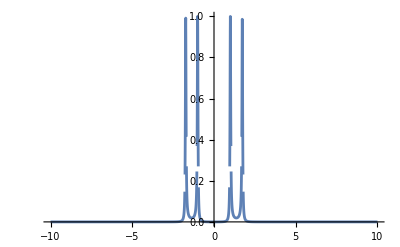

```mathematica
Plot[trans[e, 0, 1, 0.1, 0.1, 2 Pi/3], {e, -10. ,10. }, PlotRange->All]
```

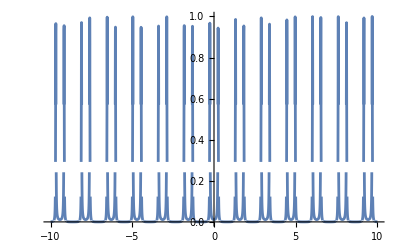

```mathematica
Plot[trans[0.5, 0, 1, 0.1, 0.1, phi], {phi, -10. ,10. }, PlotRange->All]
```

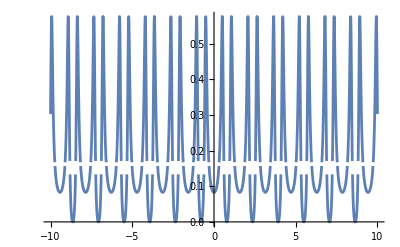

```mathematica
Plot[trans[0.5, 0, 0.5, 0.1, 0.5, phi], {phi, -10. ,10. }, PlotRange->All]
```

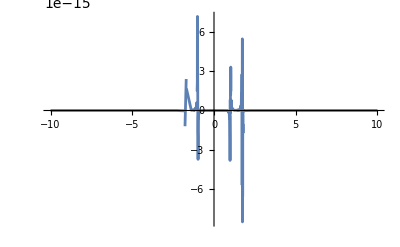

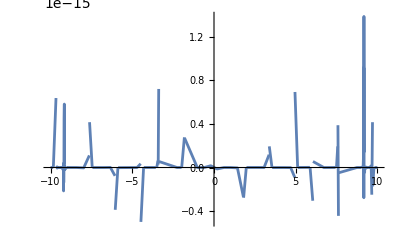

```mathematica
(*checking_Im_part*)
transIm[ϵ_, ϵ1_,t0_,  γl_, γr_,ϕ_]:=Im[(16 ⅇ^(4 ⅈ ϕ) (1+ⅇ^(4 ⅈ ϕ))^2 t0^4 γl γr (ϵ-ϵ1)^2)/((4 (-1+ⅇ^(4 ⅈ ϕ))^2 t0^4+4 ⅇ^(4 ⅈ ϕ) t0^2 (ⅈ γl+ⅈ γr+4 ϵ-4 ϵ1) (ϵ-ϵ1)+ⅇ^(4 ⅈ ϕ) (γl-2 ⅈ (ϵ-ϵ1)) (γr-2 ⅈ (ϵ-ϵ1)) (ϵ-ϵ1)^2) (4 (-1+ⅇ^(4 ⅈ ϕ))^2 t0^4-4 ⅈ ⅇ^(4 ⅈ ϕ) t0^2 (γl+γr+4 ⅈ (ϵ-ϵ1)) (ϵ-ϵ1)+ⅇ^(4 ⅈ ϕ) (γl+2 ⅈ (ϵ-ϵ1)) (γr+2 ⅈ (ϵ-ϵ1)) (ϵ-ϵ1)^2))];
Plot[transIm[e, 0, 1, 0.1, 0.1, 2 Pi/3], {e, -10. ,10. }, PlotRange->All]
Plot[transIm[0.5, 0, 1, 0.1, 0.1, phi], {phi, -10. ,10. }, PlotRange->All]
```

```mathematica
(*
Simplify@Im[(16 ⅇ^(4 ⅈ ϕ) (1+ⅇ^(4 ⅈ ϕ))^2 t0^4 γl γr (ϵ-ϵ1)^2)/((4 (-1+ⅇ^(4 ⅈ ϕ))^2 t0^4+4 ⅇ^(4 ⅈ ϕ) t0^2 (ⅈ γl+ⅈ γr+4 ϵ-4 ϵ1) (ϵ-ϵ1)+ⅇ^(4 ⅈ ϕ) (γl-2 ⅈ (ϵ-ϵ1)) (γr-2 ⅈ (ϵ-ϵ1)) (ϵ-ϵ1)^2) (4 (-1+ⅇ^(4 ⅈ ϕ))^2 t0^4-4 ⅈ ⅇ^(4 ⅈ ϕ) t0^2 (γl+γr+4 ⅈ (ϵ-ϵ1)) (ϵ-ϵ1)+ⅇ^(4 ⅈ ϕ) (γl+2 ⅈ (ϵ-ϵ1)) (γr+2 ⅈ (ϵ-ϵ1)) (ϵ-ϵ1)^2))]//ComplexExpand
*)
```

```mathematica
(*Im[(16 ⅇ^(4 ⅈ ϕ) (1+ⅇ^(4 ⅈ ϕ))^2 t0^4 γl γr (ϵ-ϵ1)^2)/((4 (-1+ⅇ^(4 ⅈ ϕ))^2 t0^4+4 ⅇ^(4 ⅈ ϕ) t0^2 (ⅈ γl+ⅈ γr+4 ϵ-4 ϵ1) (ϵ-ϵ1)+ⅇ^(4 ⅈ ϕ) (γl-2 ⅈ (ϵ-ϵ1)) (γr-2 ⅈ (ϵ-ϵ1)) (ϵ-ϵ1)^2) (4 (-1+ⅇ^(4 ⅈ ϕ))^2 t0^4-4 ⅈ ⅇ^(4 ⅈ ϕ) t0^2 (γl+γr+4 ⅈ (ϵ-ϵ1)) (ϵ-ϵ1)+ⅇ^(4 ⅈ ϕ) (γl+2 ⅈ (ϵ-ϵ1)) (γr+2 ⅈ (ϵ-ϵ1)) (ϵ-ϵ1)^2))//ComplexExpand] *)
```

```mathematica
(16 ⅇ^(4 ⅈ ϕ) (1+ⅇ^(4 ⅈ ϕ))^2 t0^4 γl γr (ϵ-ϵ1)^2)/((4 (-1+ⅇ^(4 ⅈ ϕ))^2 t0^4+4 ⅇ^(4 ⅈ ϕ) t0^2 (ⅈ γl+ⅈ γr+4 ϵ-4 ϵ1) (ϵ-ϵ1)+ⅇ^(4 ⅈ ϕ) (γl-2 ⅈ (ϵ-ϵ1)) (γr-2 ⅈ (ϵ-ϵ1)) (ϵ-ϵ1)^2) (4 (-1+ⅇ^(4 ⅈ ϕ))^2 t0^4-4 ⅈ ⅇ^(4 ⅈ ϕ) t0^2 (γl+γr+4 ⅈ (ϵ-ϵ1)) (ϵ-ϵ1)+ⅇ^(4 ⅈ ϕ) (γl+2 ⅈ (ϵ-ϵ1)) (γr+2 ⅈ (ϵ-ϵ1)) (ϵ-ϵ1)^2));
```

I divide numerator and denominator by e^8i phi.  Denoted numn and denn.

```mathematica
num=16 ⅇ^(4 ⅈ ϕ) (1+ⅇ^(4 ⅈ ϕ))^2 t0^4 γl γr (ϵ-ϵ1)^2;
numn=ExpToTrig@Expand[num/ⅇ^(8 ⅈ ϕ)];

(*re[z_] = Simplify@(z + Conjugate[z])/2;
im[z_]= (z - Conjugate[z])/(2  I);*)

numnRe=Simplify@Re@numn

numnIm =Simplify@Im@numn
```

64 t0^4 γl γr (ϵ-ϵ1)^2 Cos[2 ϕ]^2

0

```mathematica
den=(4 (-1+ⅇ^(4 ⅈ ϕ))^2 t0^4+4 ⅇ^(4 ⅈ ϕ) t0^2 (ⅈ γl+ⅈ γr+4 ϵ-4 ϵ1) (ϵ-ϵ1)+ⅇ^(4 ⅈ ϕ) (γl-2 ⅈ (ϵ-ϵ1)) (γr-2 ⅈ (ϵ-ϵ1)) (ϵ-ϵ1)^2) (4 (-1+ⅇ^(4 ⅈ ϕ))^2 t0^4-4 ⅈ ⅇ^(4 ⅈ ϕ) t0^2 (γl+γr+4 ⅈ (ϵ-ϵ1)) (ϵ-ϵ1)+ⅇ^(4 ⅈ ϕ) (γl+2 ⅈ (ϵ-ϵ1)) (γr+2 ⅈ (ϵ-ϵ1)) (ϵ-ϵ1)^2);
den1= (4 (-1+ⅇ^(4 ⅈ ϕ))^2 t0^4+4 ⅇ^(4 ⅈ ϕ) t0^2 (ⅈ γl+ⅈ γr+4 ϵ-4 ϵ1) (ϵ-ϵ1)+ⅇ^(4 ⅈ ϕ) (γl-2 ⅈ (ϵ-ϵ1)) (γr-2 ⅈ (ϵ-ϵ1)) (ϵ-ϵ1)^2) ;
den2=(4 (-1+ⅇ^(4 ⅈ ϕ))^2 t0^4-4 ⅈ ⅇ^(4 ⅈ ϕ) t0^2 (γl+γr+4 ⅈ (ϵ-ϵ1)) (ϵ-ϵ1)+ⅇ^(4 ⅈ ϕ) (γl+2 ⅈ (ϵ-ϵ1)) (γr+2 ⅈ (ϵ-ϵ1)) (ϵ-ϵ1)^2);
den1n= ExpToTrig@Expand[den1/ⅇ^(4 ⅈ ϕ)];
den2n=ExpToTrig@Expand[den2/ⅇ^(4 ⅈ ϕ)];

denn= Expand@(den1n den2n);


dennRe=FullSimplify@Re@denn
dennIm= Simplify@Im@denn


(*denRe=Simplify[re@denn,Assumptions->$Assumptions]
denIm =Simplify@im@den*)
```

96 t0^8-256 t0^6 (ϵ-ϵ1)^2+16 t0^4 (γl^2+γl γr+γr^2+20 (ϵ-ϵ1)^2) (ϵ-ϵ1)^2+(γl^2+4 (ϵ-ϵ1)^2) (γr^2+4 (ϵ-ϵ1)^2) (ϵ-ϵ1)^4-16 t0^2 (γl^2+γr^2+8 (ϵ-ϵ1)^2) (ϵ-ϵ1)^4-16 t0^4 (8 t0^4-16 t0^2 (ϵ-ϵ1)^2+(-γl γr+4 (ϵ-ϵ1)^2) (ϵ-ϵ1)^2) Cos[4 ϕ]+32 t0^8 Cos[8 ϕ]

0

```mathematica
denominator:
96 t0^8-256 t0^6 (ϵ-ϵ1)^2+16 t0^4 (γl^2+γl γr+γr^2+20 (ϵ-ϵ1)^2) (ϵ-ϵ1)^2+(γl^2+4 (ϵ-ϵ1)^2) (γr^2+4 (ϵ-ϵ1)^2) (ϵ-ϵ1)^4-16 t0^2 (γl^2+γr^2+8 (ϵ-ϵ1)^2) (ϵ-ϵ1)^4-16 t0^4 (8 t0^4-16 t0^2 (ϵ-ϵ1)^2+(-γl γr+4 (ϵ-ϵ1)^2) (ϵ-ϵ1)^2) Cos[4 ϕ]+32 t0^8 Cos[8 ϕ]

numerator:
64 t0^4 γl γr (ϵ-ϵ1)^2 Cos[2 ϕ]^2
```

denominator:96 t0^8-256 t0^6 (ϵ-ϵ1)^2+16 t0^4 (γl^2+γl γr+γr^2+20 (ϵ-ϵ1)^2) (ϵ-ϵ1)^2+(γl^2+4 (ϵ-ϵ1)^2) (γr^2+4 (ϵ-ϵ1)^2) (ϵ-ϵ1)^4-16 t0^2 (γl^2+γr^2+8 (ϵ-ϵ1)^2) (ϵ-ϵ1)^4-16 t0^4 (8 t0^4-16 t0^2 (ϵ-ϵ1)^2+(-γl γr+4 (ϵ-ϵ1)^2) (ϵ-ϵ1)^2) Cos[4 ϕ]+32 t0^8 Cos[8 ϕ]

numerator:64 t0^4 γl γr (ϵ-ϵ1)^2 Cos[2 ϕ]^2

```mathematica
Tnew=FullSimplify@(numn/denn)
```

-((64 t0^4 γl γr (ϵ-ϵ1)^2 Cos[2 ϕ]^2)/(-96 t0^8+256 t0^6 (ϵ-ϵ1)^2-16 t0^4 (γl^2+γl γr+γr^2+20 (ϵ-ϵ1)^2) (ϵ-ϵ1)^2-(γl^2+4 (ϵ-ϵ1)^2) (γr^2+4 (ϵ-ϵ1)^2) (ϵ-ϵ1)^4+16 t0^2 (γl^2+γr^2+8 (ϵ-ϵ1)^2) (ϵ-ϵ1)^4+16 t0^4 (8 t0^4-16 t0^2 (ϵ-ϵ1)^2+(-γl γr+4 (ϵ-ϵ1)^2) (ϵ-ϵ1)^2) Cos[4 ϕ]-32 t0^8 Cos[8 ϕ]))

```mathematica
-((64 t0^4 γl γr (ϵ-ϵ1)^2 Cos[2 ϕ]^2)/(-96 t0^8+256 t0^6 (ϵ-ϵ1)^2-16 t0^4 (γl^2+γl γr+γr^2+20 (ϵ-ϵ1)^2) (ϵ-ϵ1)^2-(γl^2+4 (ϵ-ϵ1)^2) (γr^2+4 (ϵ-ϵ1)^2) (ϵ-ϵ1)^4+16 t0^2 (γl^2+γr^2+8 (ϵ-ϵ1)^2) (ϵ-ϵ1)^4+16 t0^4 (8 t0^4-16 t0^2 (ϵ-ϵ1)^2+(-γl γr+4 (ϵ-ϵ1)^2) (ϵ-ϵ1)^2) Cos[4 ϕ]-32 t0^8 Cos[8 ϕ]));
```

```mathematica
denn=96 t0^8-256 t0^6 (ϵ-ϵ1)^2+16 t0^4 (γl^2+γl γr+γr^2+20 (ϵ-ϵ1)^2) (ϵ-ϵ1)^2+(γl^2+4 (ϵ-ϵ1)^2) (γr^2+4 (ϵ-ϵ1)^2) (ϵ-ϵ1)^4-16 t0^2 (γl^2+γr^2+8 (ϵ-ϵ1)^2) (ϵ-ϵ1)^4-16 t0^4 (8 t0^4-16 t0^2 (ϵ-ϵ1)^2+(-γl γr+4 (ϵ-ϵ1)^2) (ϵ-ϵ1)^2) Cos[4 ϕ]+32 t0^8 Cos[8 ϕ];



denn=Collect[denn, t0];
Listden =MonomialList[denn,t0] //MatrixForm
```

(t0^8 (96-128 Cos[4 ϕ]+32 Cos[8 ϕ])
t0^6 (-256 ϵ^2+512 ϵ ϵ1-256 ϵ1^2+256 ϵ^2 Cos[4 ϕ]-512 ϵ ϵ1 Cos[4 ϕ]+256 ϵ1^2 Cos[4 ϕ])
t0^4 (16 γl^2 ϵ^2+16 γl γr ϵ^2+16 γr^2 ϵ^2+320 ϵ^4-32 γl^2 ϵ ϵ1-32 γl γr ϵ ϵ1-32 γr^2 ϵ ϵ1-1280 ϵ^3 ϵ1+16 γl^2 ϵ1^2+16 γl γr ϵ1^2+16 γr^2 ϵ1^2+1920 ϵ^2 ϵ1^2-1280 ϵ ϵ1^3+320 ϵ1^4+16 γl γr ϵ^2 Cos[4 ϕ]-64 ϵ^4 Cos[4 ϕ]-32 γl γr ϵ ϵ1 Cos[4 ϕ]+256 ϵ^3 ϵ1 Cos[4 ϕ]+16 γl γr ϵ1^2 Cos[4 ϕ]-384 ϵ^2 ϵ1^2 Cos[4 ϕ]+256 ϵ ϵ1^3 Cos[4 ϕ]-64 ϵ1^4 Cos[4 ϕ])
t0^2 (-16 γl^2 ϵ^4-16 γr^2 ϵ^4-128 ϵ^6+64 γl^2 ϵ^3 ϵ1+64 γr^2 ϵ^3 ϵ1+768 ϵ^5 ϵ1-96 γl^2 ϵ^2 ϵ1^2-96 γr^2 ϵ^2 ϵ1^2-1920 ϵ^4 ϵ1^2+64 γl^2 ϵ ϵ1^3+64 γr^2 ϵ ϵ1^3+2560 ϵ^3 ϵ1^3-16 γl^2 ϵ1^4-16 γr^2 ϵ1^4-1920 ϵ^2 ϵ1^4+768 ϵ ϵ1^5-128 ϵ1^6)
γl^2 γr^2 ϵ^4+4 γl^2 ϵ^6+4 γr^2 ϵ^6+16 ϵ^8-4 γl^2 γr^2 ϵ^3 ϵ1-24 γl^2 ϵ^5 ϵ1-24 γr^2 ϵ^5 ϵ1-128 ϵ^7 ϵ1+6 γl^2 γr^2 ϵ^2 ϵ1^2+60 γl^2 ϵ^4 ϵ1^2+60 γr^2 ϵ^4 ϵ1^2+448 ϵ^6 ϵ1^2-4 γl^2 γr^2 ϵ ϵ1^3-80 γl^2 ϵ^3 ϵ1^3-80 γr^2 ϵ^3 ϵ1^3-896 ϵ^5 ϵ1^3+γl^2 γr^2 ϵ1^4+60 γl^2 ϵ^2 ϵ1^4+60 γr^2 ϵ^2 ϵ1^4+1120 ϵ^4 ϵ1^4-24 γl^2 ϵ ϵ1^5-24 γr^2 ϵ ϵ1^5-896 ϵ^3 ϵ1^5+4 γl^2 ϵ1^6+4 γr^2 ϵ1^6+448 ϵ^2 ϵ1^6-128 ϵ ϵ1^7+16 ϵ1^8)

```mathematica
FullSimplify@TrigFactor@Listden
```

(256 t0^8 Sin[2 ϕ]^4
-512 t0^6 (ϵ-ϵ1)^2 Sin[2 ϕ]^2
16 t0^4 (ϵ-ϵ1)^2 (γl^2+γl γr+γr^2+20 (ϵ-ϵ1)^2+(γl γr-4 (ϵ-ϵ1)^2) Cos[4 ϕ])
-16 t0^2 (γl^2+γr^2+8 (ϵ-ϵ1)^2) (ϵ-ϵ1)^4
(γl^2+4 (ϵ-ϵ1)^2) (γr^2+4 (ϵ-ϵ1)^2) (ϵ-ϵ1)^4)

```mathematica
These are the terms that denominator consists of;
({{256 t0^8 Sin[2 ϕ]^4}, {-512 t0^6 (ϵ-ϵ1)^2 Sin[2 ϕ]^2}, {16 t0^4 (ϵ-ϵ1)^2 (γl^2+γl γr+γr^2+20 (ϵ-ϵ1)^2+(γl γr-4 (ϵ-ϵ1)^2) Cos[4 ϕ])}, {-16 t0^2 (γl^2+γr^2+8 (ϵ-ϵ1)^2) (ϵ-ϵ1)^4}, {(γl^2+4 (ϵ-ϵ1)^2) (γr^2+4 (ϵ-ϵ1)^2) (ϵ-ϵ1)^4}});
The numerator is;
64 t0^4 γl γr (ϵ-ϵ1)^2 Cos[2 ϕ]^2 ;
```